## New mathematical function study

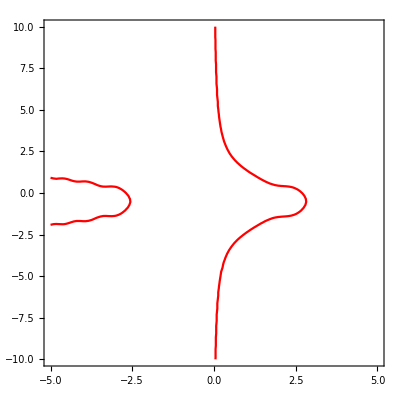

```mathematica
rad[x_]:=x*π/180;
myf[a_]:=x^2+2x*y+a*x*y^2+a*Sin[rad[15*a]*x^2]^2;
x[exp_,a_,color_]:=ContourPlot[myf[a]==a^exp,{x,-5,5},{y,-10,10},ContourStyle->color,PlotLegends->Automatic];
Show[x[3,2,Red]]
```